```mathematica
q=175
spinx[k_]:=Table[(KroneckerDelta[i,j+1]+KroneckerDelta[i+1,j])/2*Sqrt[k*(k+1)-i*j],{i,-k,k},{j,-k,k}]
spiny[k_]:=Table[(KroneckerDelta[i,j+1]-KroneckerDelta[i+1,j])/I/2*Sqrt[k*(k+1)-i*j],{i,-k,k},{j,-k,k}]
spinz[k_]:=Table[(KroneckerDelta[i,j])*i,{i,-k,k},{j,-k,k}]
$Assumptions=Element[t,Reals];
```

175

(5741/2-4.2045 b-(3 Cos[θ]^2)/2 | 0. | 0. | 0.-3 ((Cos[ϕ]^2 Sin[θ]^2)/(2 √2)-(Sin[θ]^2 Sin[ϕ]^2)/(2 √2)) | 0. | 0.
0. | 5739/2-1.4015 b+(3 Cos[θ]^2)/2 | 0.707107-3 ((Cos[ϕ]^2 Sin[θ]^2)/(2 √2)+(Sin[θ]^2 Sin[ϕ]^2)/(2 √2)) | 0. | 0. | 0.
0. | 0.707107-3 ((Cos[ϕ]^2 Sin[θ]^2)/(2 √2)+(Sin[θ]^2 Sin[ϕ]^2)/(2 √2)) | 0.-1.4015 b | 0. | 0. | 0.-3 ((Cos[ϕ]^2 Sin[θ]^2)/(2 √2)-(Sin[θ]^2 Sin[ϕ]^2)/(2 √2))
0.-3 ((Cos[ϕ]^2 Sin[θ]^2)/(2 √2)-(Sin[θ]^2 Sin[ϕ]^2)/(2 √2)) | 0. | 0. | 0.+1.4015 b | 0.707107-3 ((Cos[ϕ]^2 Sin[θ]^2)/(2 √2)+(Sin[θ]^2 Sin[ϕ]^2)/(2 √2)) | 0.
0. | 0. | 0. | 0.707107-3 ((Cos[ϕ]^2 Sin[θ]^2)/(2 √2)+(Sin[θ]^2 Sin[ϕ]^2)/(2 √2)) | 5739/2+1.4015 b+(3 Cos[θ]^2)/2 | 0.
0. | 0. | 0.-3 ((Cos[ϕ]^2 Sin[θ]^2)/(2 √2)-(Sin[θ]^2 Sin[ϕ]^2)/(2 √2)) | 0. | 0. | 5741/2+4.2045 b-(3 Cos[θ]^2)/2)

(717.625 | 0. | 0. | 0.397748 | 0. | 0.
0. | 2152.38 | -0.0883883 | 0. | 0. | 0.
0. | -0.0883883 | -717.5 | 0. | 0. | 0.397748
0.397748 | 0. | 0. | 717.5 | -0.0883883 | 0.
0. | 0. | 0. | -0.0883883 | 3587.38 | 0.
0. | 0. | 0.397748 | 0. | 0. | 5022.63)

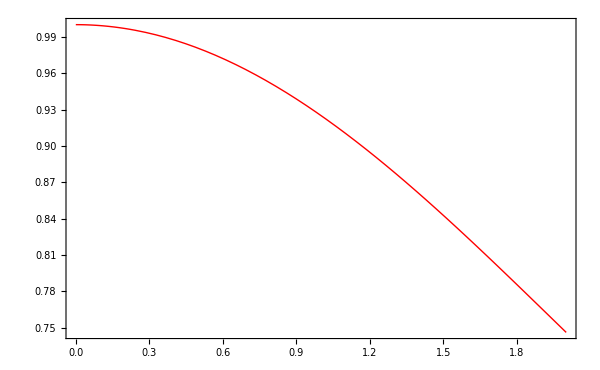

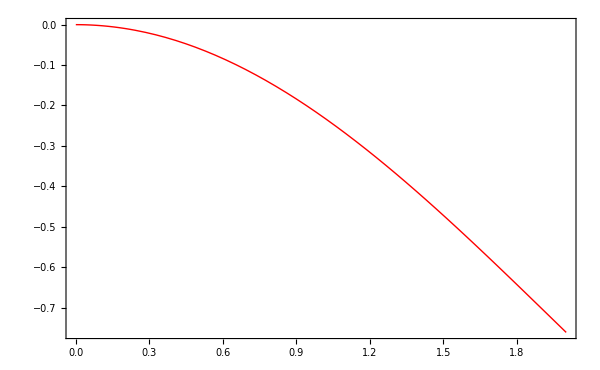

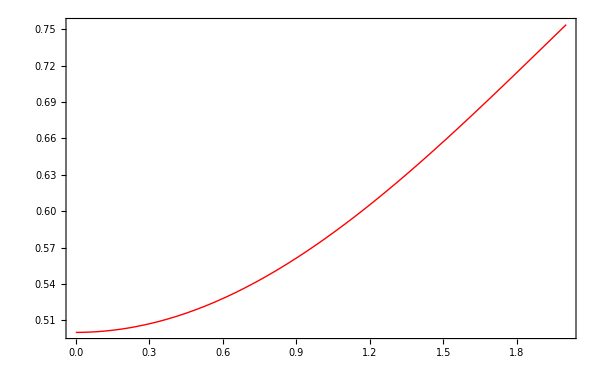

```mathematica
r={Cos[θ],Sin[θ]*Cos[ϕ],Sin[θ]*Sin[ϕ]};
tabnv={spinz[1],spinx[1],spiny[1]};
tabp1={spinz[1/2],spinx[1/2],spiny[1/2]};
tabnv=(KroneckerProduct[#,IdentityMatrix[2]]&)/@(r*tabnv);
tabp1=(KroneckerProduct[IdentityMatrix[3],(#)]&)/@(r*tabp1);
zeem=KroneckerProduct[spinz[1],IdentityMatrix[2]]*γ*b+KroneckerProduct[spinz[1].spinz[1],IdentityMatrix[2]]*d+γ*b*KroneckerProduct[IdentityMatrix[3],spinz[1/2]];
dipol=KroneckerProduct[spinx[1],IdentityMatrix[2]].KroneckerProduct[IdentityMatrix[3],spinx[1/2]]+KroneckerProduct[spiny[1],IdentityMatrix[2]].KroneckerProduct[IdentityMatrix[3],spiny[1/2]]+KroneckerProduct[spinz[1],IdentityMatrix[2]].KroneckerProduct[IdentityMatrix[3],spinz[1/2]]-3*Total[MapThread[#1.#2&,{tabnv,tabp1}]];
mag=(KroneckerProduct[spinx[1],IdentityMatrix[2]]*Ω+KroneckerProduct[IdentityMatrix[3],spinx[1/2]]*Ω*Sqrt[2])*Cos[ω*t];
(hameff=zeem+dipol)//MatrixForm
nvp=spinx[1]+I*spiny[1];
nvm=spinx[1]-I*spiny[1];
p1p=spinx[1/2]+I*spiny[1/2];
p1m=spinx[1/2]-I*spiny[1/2];
ρ=KroneckerProduct[DiagonalMatrix[{0,1,0}],IdentityMatrix[2]];
ρ=ρ/Tr[ρ];
d=2870;
γ=2.803;
ham2=hameff/.θ->Pi/3/.ϕ->Pi/3/.b->d/γ/2;
ham2//MatrixForm
rhosol=MatrixExp[-I*ham2*t].ρ.MatrixExp[I*ham2*t];
rhosol=Chop[rhosol];
Plot[Tr[DiagonalMatrix[{0,0,1,1,0,0}].rhosol]/.d->2870,{t,0,2.001}]
Plot[Tr[spinz[5/2].rhosol//Chop],{t,0,2.001}]
Plot[Tr[DiagonalMatrix[{1,0,1,0,1,0}].rhosol],{t,0,2.001}]
```

```mathematica
Clear[All]
```

```mathematica
dipol+mag//MatrixForm
```

(1/2-(3 Cos[θ]^2)/2 | 1/2 Ω Cos[t ω] | (Ω Cos[t ω])/(√2) | -3 ((Cos[ϕ]^2 Sin[θ]^2)/(2 √2)-(Sin[θ]^2 Sin[ϕ]^2)/(2 √2)) | 0 | 0
1/2 Ω Cos[t ω] | -1/2+(3 Cos[θ]^2)/2 | 1/(√2)-3 ((Cos[ϕ]^2 Sin[θ]^2)/(2 √2)+(Sin[θ]^2 Sin[ϕ]^2)/(2 √2)) | (Ω Cos[t ω])/(√2) | 0 | 0
(Ω Cos[t ω])/(√2) | 1/(√2)-3 ((Cos[ϕ]^2 Sin[θ]^2)/(2 √2)+(Sin[θ]^2 Sin[ϕ]^2)/(2 √2)) | 0 | 1/2 Ω Cos[t ω] | (Ω Cos[t ω])/(√2) | -3 ((Cos[ϕ]^2 Sin[θ]^2)/(2 √2)-(Sin[θ]^2 Sin[ϕ]^2)/(2 √2))
-3 ((Cos[ϕ]^2 Sin[θ]^2)/(2 √2)-(Sin[θ]^2 Sin[ϕ]^2)/(2 √2)) | (Ω Cos[t ω])/(√2) | 1/2 Ω Cos[t ω] | 0 | 1/(√2)-3 ((Cos[ϕ]^2 Sin[θ]^2)/(2 √2)+(Sin[θ]^2 Sin[ϕ]^2)/(2 √2)) | (Ω Cos[t ω])/(√2)
0 | 0 | (Ω Cos[t ω])/(√2) | 1/(√2)-3 ((Cos[ϕ]^2 Sin[θ]^2)/(2 √2)+(Sin[θ]^2 Sin[ϕ]^2)/(2 √2)) | -1/2+(3 Cos[θ]^2)/2 | 1/2 Ω Cos[t ω]
0 | 0 | -3 ((Cos[ϕ]^2 Sin[θ]^2)/(2 √2)-(Sin[θ]^2 Sin[ϕ]^2)/(2 √2)) | (Ω Cos[t ω])/(√2) | 1/2 Ω Cos[t ω] | 1/2-(3 Cos[θ]^2)/2)

```mathematica
hameff=hameff/.θ->Pi/3/.ϕ->Pi/3.
hameff+mag//MatrixForm
rotwav=MatrixExp[-I*DiagonalMatrix[Diagonal[hameff]]*t];
b=d/γ/2;
(rwaham=Refine[ConjugateTranspose[rotwav].(hameff+mag).rotwav-I*ConjugateTranspose[rotwav].D[rotwav,t]]);
```

{{22961/8-4.2045 b,0.,0.,0.397748,0.,0.},{0.,22959/8-1.4015 b,-0.0883883,0.,0.,0.},{0.,-0.0883883,0.-1.4015 b,0.,0.,0.397748},{0.397748,0.,0.,0.+1.4015 b,-0.0883883,0.},{0.,0.,0.,-0.0883883,22959/8+1.4015 b,0.},{0.,0.,0.397748,0.,0.,22961/8+4.2045 b}}

(22961/8-4.2045 b | 0.+(Ω Cos[t ω])/(√2) | 0.+(Ω Cos[t ω])/(√2) | 0.397748 | 0. | 0.
0.+(Ω Cos[t ω])/(√2) | 22959/8-1.4015 b | -0.0883883 | 0.+(Ω Cos[t ω])/(√2) | 0. | 0.
0.+(Ω Cos[t ω])/(√2) | -0.0883883 | 0.-1.4015 b | 0.+(Ω Cos[t ω])/(√2) | 0.+(Ω Cos[t ω])/(√2) | 0.397748
0.397748 | 0.+(Ω Cos[t ω])/(√2) | 0.+(Ω Cos[t ω])/(√2) | 0.+1.4015 b | -0.0883883 | 0.+(Ω Cos[t ω])/(√2)
0. | 0. | 0.+(Ω Cos[t ω])/(√2) | -0.0883883 | 22959/8+1.4015 b | 0.+(Ω Cos[t ω])/(√2)
0. | 0. | 0.397748 | 0.+(Ω Cos[t ω])/(√2) | 0.+(Ω Cos[t ω])/(√2) | 22961/8+4.2045 b)

```mathematica
d/2
```

```mathematica
Diagonal[hameff]
```

{717.625,2152.38,-717.5,717.5,3587.38,5022.63}

{717.625,2152.38,-717.5,717.5,3587.38,5022.63}

```mathematica
zeem/.b->d/γ/2//MatrixForm
```

(717.5 | 0. | 0. | 0. | 0. | 0.
0. | 2152.5 | 0. | 0. | 0. | 0.
0. | 0. | -717.5 | 0. | 0. | 0.
0. | 0. | 0. | 717.5 | 0. | 0.
0. | 0. | 0. | 0. | 3587.5 | 0.
0. | 0. | 0. | 0. | 0. | 5022.5)

```mathematica
mag//MatrixForm
```

(0 | 1/2 Ω Cos[t ω] | (Ω Cos[t ω])/(√2) | 0 | 0 | 0
1/2 Ω Cos[t ω] | 0 | 0 | (Ω Cos[t ω])/(√2) | 0 | 0
(Ω Cos[t ω])/(√2) | 0 | 0 | 1/2 Ω Cos[t ω] | (Ω Cos[t ω])/(√2) | 0
0 | (Ω Cos[t ω])/(√2) | 1/2 Ω Cos[t ω] | 0 | 0 | (Ω Cos[t ω])/(√2)
0 | 0 | (Ω Cos[t ω])/(√2) | 0 | 0 | 1/2 Ω Cos[t ω]
0 | 0 | 0 | (Ω Cos[t ω])/(√2) | 1/2 Ω Cos[t ω] | 0)

```mathematica
rwaham2//MatrixForm
```

(2152.25-4.2045 b-3/8 ⅇ^(-2 ⅈ θ)-3/8 ⅇ^(2 ⅈ θ) | 0.353553 Ω | 0.353553 Ω | 0.132583 ⅇ^(-2 ⅈ (θ+ϕ))+0.132583 ⅇ^(2 ⅈ (θ+ϕ))-0.265165 ⅇ^(2 ⅈ θ-2 ⅈ (θ+ϕ))+0.132583 ⅇ^(4 ⅈ θ-2 ⅈ (θ+ϕ))+0.132583 ⅇ^(4 ⅈ ϕ-2 ⅈ (θ+ϕ))-0.265165 ⅇ^(-2 ⅈ (θ+ϕ)+2 ⅈ (θ+2 ϕ)) | 0 | 0
0.353553 Ω | 717.75-1.4015 b+3/8 ⅇ^(-2 ⅈ θ)+3/8 ⅇ^(2 ⅈ θ) | 0 | 0.353553 Ω | 0 | 0
0.353553 Ω | 0 | 717.5-1.4015 b | 0.353553 Ω | 0 | 0
(3 ⅇ^(-2 ⅈ θ-2 ⅈ ϕ))/(16 √2)+(3 ⅇ^(2 ⅈ θ-2 ⅈ ϕ))/(16 √2)+(3 ⅇ^(-2 ⅈ θ+2 ⅈ ϕ))/(16 √2)+(3 ⅇ^(2 ⅈ θ+2 ⅈ ϕ))/(16 √2)-(3 ⅇ^(-2 ⅈ ϕ))/(8 √2)-(3 ⅇ^(2 ⅈ ϕ))/(8 √2) | 0.353553 Ω | 0.353553 Ω | -717.5+1.4015 b | 0 | 0
0 | 0 | 0 | 0 | -717.25+1.4015 b+3/8 ⅇ^(-2 ⅈ θ)+3/8 ⅇ^(2 ⅈ θ) | 0.353553 Ω
0 | 0 | 0 | 0 | 0.353553 Ω | -2152.75+4.2045 b-3/8 ⅇ^(-2 ⅈ θ)-3/8 ⅇ^(2 ⅈ θ))

{{ⅇ^((0.-717.5 ⅈ) t),0,0,0,0,0},{0,ⅇ^((0.-2152.5 ⅈ) t),0,0,0,0},{0,0,ⅇ^((0.+717.5 ⅈ) t),0,0,0},{0,0,0,ⅇ^((0.-717.5 ⅈ) t),0,0},{0,0,0,0,ⅇ^((0.-3587.5 ⅈ) t),0},{0,0,0,0,0,ⅇ^((0.-5022.5 ⅈ) t)}}

{{ⅇ^((0.-717.5 ⅈ) t),0,0,0,0,0},{0,ⅇ^((0.-2152.5 ⅈ) t),0,0,0,0},{0,0,ⅇ^((0.+717.5 ⅈ) t),0,0,0},{0,0,0,ⅇ^((0.-717.5 ⅈ) t),0,0},{0,0,0,0,ⅇ^((0.-3587.5 ⅈ) t),0},{0,0,0,0,0,ⅇ^((0.-5022.5 ⅈ) t)}}

(717.625 | 0.+(Ω Cos[t ω])/(√2) | 0.+(Ω Cos[t ω])/(√2) | 0.397748 | 0. | 0.
0.+(Ω Cos[t ω])/(√2) | 2152.38 | -0.0883883 | 0.+(Ω Cos[t ω])/(√2) | 0. | 0.
0.+(Ω Cos[t ω])/(√2) | -0.0883883 | -717.5 | 0.+(Ω Cos[t ω])/(√2) | 0.+(Ω Cos[t ω])/(√2) | 0.397748
0.397748 | 0.+(Ω Cos[t ω])/(√2) | 0.+(Ω Cos[t ω])/(√2) | 717.5 | -0.0883883 | 0.+(Ω Cos[t ω])/(√2)
0. | 0. | 0.+(Ω Cos[t ω])/(√2) | -0.0883883 | 3587.38 | 0.+(Ω Cos[t ω])/(√2)
0. | 0. | 0.397748 | 0.+(Ω Cos[t ω])/(√2) | 0.+(Ω Cos[t ω])/(√2) | 5022.63)

(0.125 | 0.353553 Ω | 0.353553 Ω | 0.397748 | 0 | 0
0.353553 Ω | -0.125 | 0. | 0.353553 Ω | 0 | 0
0.353553 Ω | 0. | 0 | 0.353553 Ω | 0 | 0.
0.397748 | 0.353553 Ω | 0.353553 Ω | 0 | 0. | 0
0 | 0 | 0 | 0. | -0.125 | 0.353553 Ω
0 | 0 | 0. | 0 | 0.353553 Ω | 0.125)

{{0.125,0.,0.,0.397748,0,0},{0.,-0.125,0.,0.,0,0},{0.,0.,0,0.,0,0.},{0.397748,0.,0.,0,0.,0},{0,0,0,0.,-0.125,0.},{0,0,0.,0,0.,0.125}}

-Graphics-

-Graphics-

{{0.125,1.76777,1.76777,0.397748,0,0},{1.76777,-0.125,0.,1.76777,0,0},{1.76777,0.,0,1.76777,0,0.},{0.397748,1.76777,1.76777,0,0.,0},{0,0,0,0.,-0.125,1.76777},{0,0,0.,0,1.76777,0.125}}

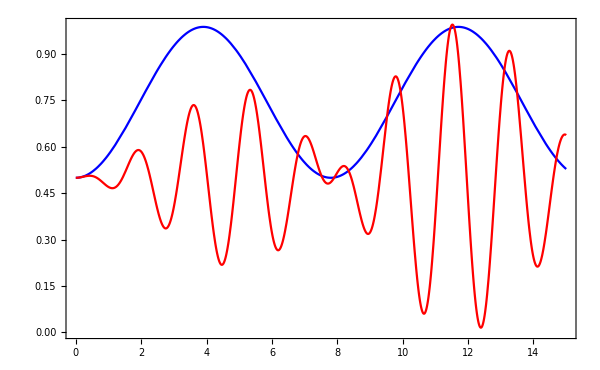

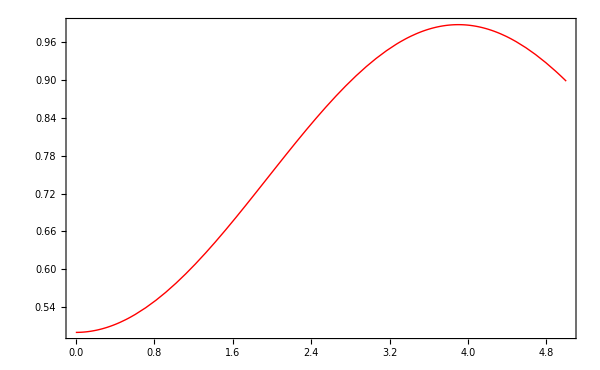

```mathematica
rotham=MatrixExp[-I*DiagonalMatrix[Diagonal[zeem/.b->(d/γ/2)]]*t]
rotwav=rotham
(rwaham=Refine[ConjugateTranspose[rotwav].(hameff+mag).rotwav-I*ConjugateTranspose[rotwav].D[rotwav,t]]);
$Assumptions=Element[t,Reals];
hameff+mag//MatrixForm
rwaham=Refine[rwaham,Element[t,Reals]]/.ω->1435//Simplify//TrigToExp//Simplify//Expand//Chop;
(rwaham2=Map[If[FreeQ[#,t],#,0]&,rwaham//Expand,{3}])//MatrixForm
rwaham3=rwaham2/.b->d/γ/2/.Ω->0
rhosol1=MatrixExp[-I*rwaham3*t].ρ.MatrixExp[I*rwaham3*t]//Chop;
Plot[Tr[DiagonalMatrix[{0,0,1,1,0,0}].rhosol]/.d->2870,{t,0,2.001}]
Plot[Tr[DiagonalMatrix[{1,0,1,0,1,0}].rhosol],{t,0,2.001}]
rwaham3=rwaham2/.b->d/γ/2/.Ω->5
rhosol2=MatrixExp[-I*rwaham3*t].ρ.MatrixExp[I*rwaham3*t]//Chop;
dat=Chop[(Tr[DiagonalMatrix[{1,0,1,0,1,0}].#]&)]/@{Chop@rhosol1,Chop@rhosol2};
Plot[dat,{t,0,15.001},PlotStyle->{Blue,Red}]
Plot[Tr[DiagonalMatrix[{1,0,1,0,1,0}].rhosol]//Chop,{t,0,5.001}]
```